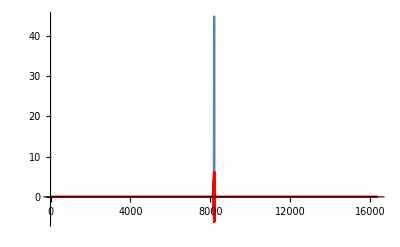

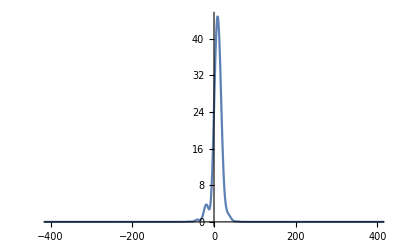

-Graphics-

```mathematica
(*Units will be nm, fs - inspiration from https://www.phys.ksu.edu/personal/washburn/Teaching/Class%20Files/NQO/Tutorials/Tutorial8_FFT.pdf*)
c=300;
lambda0=800; (*Central wavelength in nm*)

w0 = 2*π*c/lambda0  ;
lTow[l_]:=2*π*c/l;


a1=-10;
a2=-00100;
a3=1000;
a4=0;

phi[w_]:= -(a1*(w-w0)+a2/2*(w-w0)^2+a3/6*(w-w0)^3+a3/24*(w-w0)^4);
A[w_] := Exp[-((w-w0)/(lTow[750]-lTow[800]))^6];
spectral[w_]:=A[w]*Exp[ⅈ*phi[w]];

Plot[A[lTow[l]],{l,700,900}];

num=2^14; (*steps to divide by*)
range = 20000 ;(*time in fs*)
δt = range/num;
δw =2π/(num*δt);

time = Table[(j-(num/2))*δt,{j,1,num}];
freq = Table[(j-(num/2))*δw,{j,1,num}];
absfreq = Table[freq[[j]]+w0,{j,1,num}];

ewdata =Table[spectral[absfreq[[j]]],{j,1,num}];
etdata = Chop[RotateRight[InverseFourier[ewdata],num/2]];
Itdata = etdata*Conjugate[etdata];

Show[ListLinePlot[Itdata],ListLinePlot[Re[etdata],PlotStyle->Red],PlotRange->{Automatic,All}]
ListLinePlot[Table[{time[[j]],Itdata[[j]]},{j,1,num}],PlotRange->{{-400,400},All},FrameLabel->{"Time (fs)","Intensity a.u."}]
```